# 20 October 2022 Notes

Peter Cullen Burbery

Abstract

## Section

## Probability

The probability at any point is 0.

```mathematica
Integrate[Piecewise[{{0.15 ⅇ^(-0.15(x-0.5)), x>=0.5}, {0, x<0.5}}],x]
```

Piecewise[{{0., x≤0.5}, {1.-1.07788 ⅇ^(-0.15 x), True}}]

```mathematica
PiecewiseExpand[Piecewise[{{0.,x≤0.5}},0.9999999999999999-1.0778841508846315 ⅇ^(-0.15 x)]]
```

Piecewise[{{0., x≤0.5}, {1. ⅇ^(-0.15 x) (-1.07788+1. ⅇ^(0.15 x)), True}}]

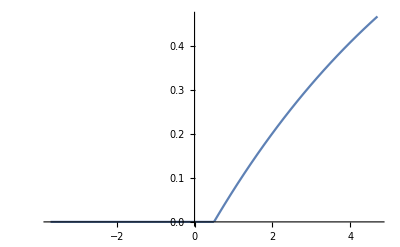

```mathematica
Plot[Piecewise[{{0.,x≤0.5}},0.9999999999999999 ⅇ^(-0.15 x) (-1.0778841508846317+1. ⅇ^(0.15 x))],{x,-3.7,4.7}]
```

```mathematica
Plot[Piecewise[{{0.,x≤0.5}},0.9999999999999999 ⅇ^(-0.15 x) (-1.0778841508846317+1. ⅇ^(0.15 x))],{x,-3.7,4.7}]
```

-Graphics-

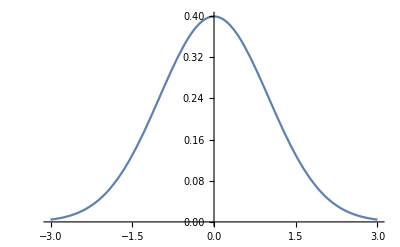

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-3,3}]
```

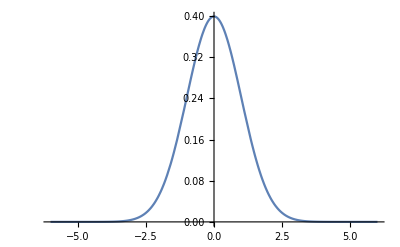

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-6,6}]
```

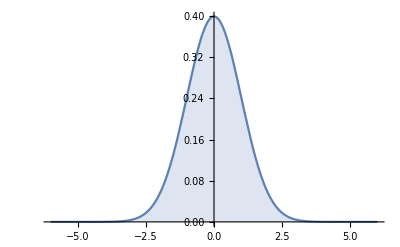

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-6,6},Filling->Bottom]
```

```mathematica
PDF[NormalDistribution[]]
```

Function[x,(ⅇ^(-x^2/2))/(√(2 π))]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[PDF[NormalDistribution[],x],{x,-∞,∞}]
```

1

∫_(-∞)^∞ pdfⅆx

μ=∫_(-∞)^∞ P(x)xⅆx

Replace the sum Σ with integral ∫■ⅆ□ from -∞ to ∞.

V (x)=E(x^2)-μ^2

f(x)=Piecewise[{{□, □}, {□, □}}]

Range of x is between 1 and 1/2.

when x is between 0 and 1/2.

```mathematica
Integrate[2,{x,0,1/2}]
```

1

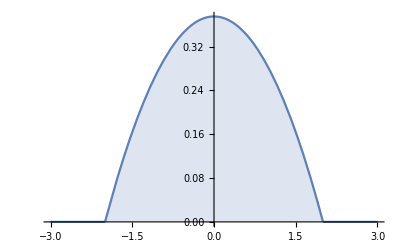

```mathematica
Plot[Piecewise[{{0.09375(4-x^2), -2<=x<=2}, {0, True}}],{x,-3,3},Filling->Bottom]
```

```mathematica
Plot[Piecewise[{{3/32(4-x^2), -2<=x<=2}, {0, True}}],{x,-3,3},Filling->Bottom]
```

-Graphics-

```mathematica
Integrate[3/32(4-x^2),{x,-2,2}]
```

1

```mathematica
Inactive[Integrate][3/32(4-x^2),{x,-2,2}]
```

3/32 (4-x^2)x-22

```mathematica
Activate[3/32 (4-x^2)x-22,Unevaluated[Integrate]]
```

1

```mathematica
∫_-2^2 (3/32(4-x^2))ⅆx
```

1

```mathematica
Integrate[Boole[3/32(4-x^2)],{x,-∞,∞}]
```

∫_(-∞)^∞ Boole[3/32 (4-x^2)]ⅆx

```mathematica
Inactive[Integrate][3/32(4-x^2),x]
```

3/32 (4-x^2)x

```mathematica
Activate[3/32 (4-x^2)x,Unevaluated[Integrate]]
```

-3/32 (-4 x+x^3/3)

```mathematica
Simplify[-3/32 (-4 x+x^3/3)]
```

-1/32 x (-12+x^2)

```mathematica
pdf=Function[x,Simplify[-3/32 (-4 x+x^3/3)]]
```

Function[x,Simplify[1/32 (-3) (-4 x+x^3/3)]]

```mathematica
pdf[-1]
```

-11/32

```mathematica
pdf[1]
```

11/32

```mathematica
pdf[1]-pdf[-1]
```

11/16

```mathematica
pdf[0.5]-pdf[-0.5]
```

0.367188

```mathematica
Inactive[Integrate][k x^2,x]
```

k x^2x

```mathematica
Activate[k x^2x,Unevaluated[Integrate]]
```

(k x^3)/3

```mathematica
Solve[Activate[k x^2x,Unevaluated[Integrate]]==1,k]
```

{{k→3/x^3}}

```mathematica
Inactive[Integrate][k x^2,x]/.First[Solve[Activate[k x^2x,Unevaluated[Integrate]]==1,k]]
```

3/xx

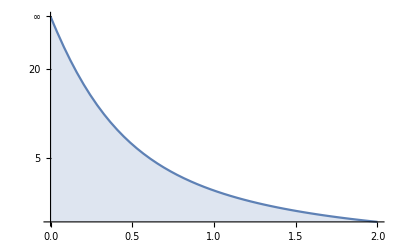

```mathematica
Plot[3/x,{x,0,2},Filling->Bottom,ScalingFunctions->{Automatic,"Infinite"}]
```

```mathematica
Inactive[Integrate][k x^2,{x,0,2}]
```

k x^2x02

```mathematica
Activate[Inactive[Integrate][k x^2,{x,0,2}]]
```

(8 k)/3

```mathematica
Solve[Activate[Inactive[Integrate][k x^2,{x,0,2}]]==1,k]
```

{{k→3/8}}

```mathematica
pdf=Function[x,3/8 x^2]
```

Function[x,(3 x^2)/8]

```mathematica
pdf[1]
```

3/8

```mathematica
pdf[0]
```

0

```mathematica
pdf[1]-pdf[0]
```

3/8

```mathematica
pdf[1.5]
```

0.84375

```mathematica
Rationalize[pdf[1.5]]
```

27/32

```mathematica
pdf[1]
```

3/8

```mathematica
pdf[1.5]-pdf[1]
```

0.46875

```mathematica
Rationalize[pdf[1.5]-pdf[1]]
```

15/32

```mathematica
pdf[2]-pdf[1.5]
```

0.65625

```mathematica
Integrate[x (3/8 x^2),{x,0,2}]
```

3/2

```mathematica
Integrate[x^2(3/8 x^2),{x,0,2}]
```

12/5

```mathematica
Integrate[x^2(3/8 x^2),{x,0,2}]-Integrate[x (3/8 x^2),{x,0,2}]^2
```

3/20

```mathematica
√20
```

2 √5

```mathematica
MinimalPolynomial[2 √5,x]
```

-20+x^2